```mathematica
Clear[rho]
rho[tau_, mu_] = E^(mu/tau) (tau)^(-3/2) ;
Manipulate[
Plot[
rho[tau, mu], 
{tau, r, 10}, 
(*PlotRange->Full,*)
AxesLabel -> {Text["k_BT"], Subscript[ρ, Text["μ = "<>ToString[mu]]] / (h/Sqrt[ Text["(2 π m)"]])^3}
],
{{r, 0.2},0.01,2},
{mu,0.1,5}
]
```

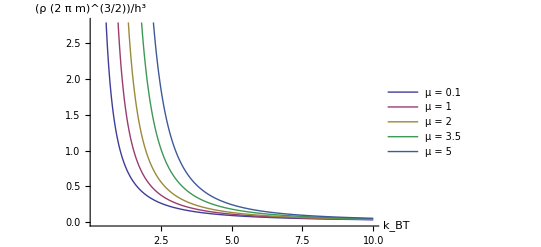

```mathematica
(* weird.  If this is moved into the cell above the placed legends don't work? *)

Plot[
Evaluate[Map[
rho[tau, #] &, {0.1, 1, 2, 3.5, 5}]], 
{tau, 0.2, 10}, 
AxesLabel -> {Text["k_BT"], ρ / (h/Sqrt[ Text["(2 π m)"]])^3},
PlotLegends->Placed[Map[Text[ "μ = "  <> ToString[#]]&, {0.1, 1, 2, 3.5, 5}], {Right,Top}]
]
```

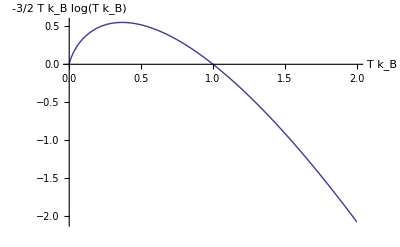

```mathematica
Plot[ 
- (3 tau/2) Log[tau], 
{tau, 0, 2},
AxesLabel->{Subscript[k, B] T, - 3 Subscript[k, B] T Log[Subscript[k, B] T]/2}]
```